# Integrating Periodic Functions

## Jeremy Jorgensen

The purpose of this notebook is to see if one of Baldereschi’s assumptions breaks down when integrating metals (or discontinuous functions). This will be achieved by comparing to the value of the first coefficient in the basis expansion of the function to the value of the exact integration of the discontinuous function.

- Define two periodic functions, one smooth and one discontinuous.
- Perform a basis expansion in plane waves.
- Compare Exact integration to first Fourier coefficient.

### Define a continuous and discontinuous function.

```mathematica
Cont[x_]:=2Exp[Cos[π x]]
Dis[x_]:= Piecewise[{{0,x<-1/2},{2Exp[Cos[π x]],Abs[x]≤1/2},{0,x>1/2}},{x,-1,1}]
```

### Plot the functions.

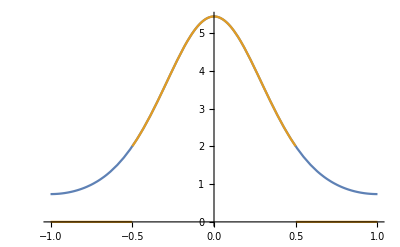

```mathematica
Plot[{Cont[x],Dis[x]},{x,-1,1}]
```

### Determine their exact integrals.

```mathematica
ContSol=Integrate[Cont[x],{x,-1,1}]//N
DiscontSol=Integrate[Dis[x],{x,-1,1}]//N
```

5.06426

3.95262

### Fourier expand the functions.

Odd terms are excluded since the function has even symmetry.

```mathematica
Basis[n_,x_]:=Cos[n π x];
nBasis=10;
```

```mathematica
ContCoeffs=Table[Integrate[Cont[x] Basis[n,x],{x,-1,1}],{n,0,nBasis-1}]//N;
ContCoeffs⟦1⟧=ContCoeffs⟦1⟧/2;
```

```mathematica
DisCoeffs=Table[Integrate[Dis[x] Basis[n,x],{x,-1,1}],{n,0,nBasis-1}];
DisCoeffs⟦1⟧=DisCoeffs⟦1⟧/2;
```

```mathematica
ContExp[x_]:=ContCoeffs.Basis[Range[0,nBasis-1] ,x]
DisExp[x_]:=DisCoeffs.Basis[Range[0,nBasis-1],x]
```

### Plot the Fourier expansion of the functions.

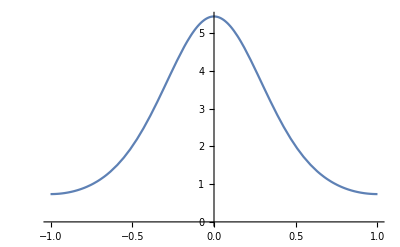

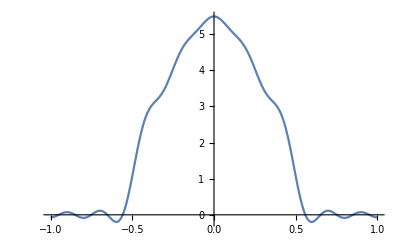

```mathematica
Plot[ContExp[x],{x,-1,1}]
Plot[DisExp[x],{x,-1,1}]
```

The first Fourier coefficients are the same as the integrals, but this really isn’t what we do in practice. We may have a smooth, periodic function and we choose to integrate it over part of its domain.

### The Mean-Value Point

The mean-value point is the point at which the leading terms in the expansion evaluate to zero. In 3D Baldereschi had to solve a system of 3 equations. In 1D we solve a single equation that makes the leading term evaluate to 0.

```mathematica
MVError[basis_,m_]:=Module[{},
meanvaluepoint=FindRoot[basis[m,x]==0,{x,.1}]⟦1⟧//Values;
MVerrorCont=(ContSol-ContExp[meanvaluepoint])/ContSol;
MVerrorDis=(DiscontSol - DisExp[meanvaluepoint])/DiscontSol;
{MVerrorCont,MVerrorDis}
];
```

### The Chadi-Cohen Points

```mathematica
pointgroups={1,-1};
addpoints[pointlist_,m_]:=Module[{newpoint},
newpointlist=pointlist//Abs;
For[i=1,i≤Length[pointlist]-1,i++,
For[j=i+1,j≤Length[pointlist],j++,
For[k=1,k≤Length[pointgroups],k++,
newpoint=pointlist⟦i⟧+pointgroups⟦k⟧pointlist⟦j⟧//Abs;
While[newpoint>1,newpoint=Abs[newpoint-2]];
If[MemberQ[newpointlist,newpoint]==True,Nothing,AppendTo[newpointlist,newpoint]];
];
];
];
newpointlist
];
CCError[basis_,m_]:=Module[{},
$Assumptions=Table[C[i]==0,{i,1,2}];
WeightCond[p_]:=Sum[Subscript[α, n],{n,1,p}]==1;
PointCond[thebasis_,p_]:=Table[Sum[Subscript[α, i] thebasis[k, Subscript[x, i]],{i,1,p}]==0,{k,1,2p-1}];
Points[p_]:=Table[Subscript[x, i],{i,1,p}];
Weight[p_]:=Table[Subscript[α, i],{i,1,p}];
If[m≤2,
unknowns=Solve[Join[{WeightCond[m]},PointCond[basis,m]],Join[Weight[m],Points[m]]]//Simplify;
unknowns=unknowns⟦1⟧//Values;
points=unknowns⟦m+1;;2m⟧;
CCerrorCont=(Sum[unknowns⟦i⟧ContExp[unknowns⟦m+i⟧],{i,1,m}]-ContSol)/ContSol//Abs;
CCerrorDis=(Sum[unknowns⟦i⟧DisExp[unknowns⟦m+i⟧],{i,1,m}]-DiscontSol)/DiscontSol//Abs; 
,
(*It finds the first two points to begin with. It times out with more than 3.*)
unknowns=Solve[Join[{WeightCond[2]},PointCond[basis,2]],Join[Weight[2],Points[2]]]//Simplify;
unknowns=unknowns⟦1⟧//Values;
points=unknowns⟦3;;4⟧//Abs;
While[Length[points]<m,points=addpoints[points,m]];
lenpts=Length[points];
weights=Table[1/lenpts,{i,1,lenpts}];
unknowns=Join[weights,points];
CCerrorCont=(Sum[unknowns⟦i⟧ContExp[unknowns⟦lenpts+i⟧],{i,1,lenpts}]-ContSol)/ContSol//Abs;
CCerrorDis=(Sum[unknowns⟦i⟧DisExp[unknowns⟦lenpts+i⟧],{i,1,lenpts}]-DiscontSol)/DiscontSol//Abs;
];
{Length[points],CCerrorCont,CCerrorDis}
];
```

```mathematica
npts=2^#&/@Range[0,2]
```

{1,2,4}

```mathematica
MVdata=MVError[Basis,1]//Timing
CCdata=Timing[CCError[Basis,#]]&/@npts
```

{0.007566,{0.605076,0.729184}}

$Aborted

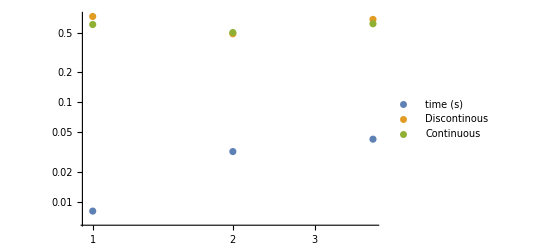

```mathematica
CCpoints=#⟦2,1⟧&/@CCdata;
CCtimes=#⟦1⟧&/@CCdata;
CCcont=#⟦2,2⟧&/@CCdata;
CCdis=#⟦2,3⟧&/@CCdata;
ListLogLogPlot[{Transpose[{CCpoints,CCtimes}],Transpose[{CCpoints,CCdis}],Transpose[{CCpoints,CCcont}]},PlotLegends->{"time (s)", "Discontinous", "Continuous"}]
```

```mathematica
u[q_]:=(2#-q-1)/(2q)&/@Range[q];
```

### Testing

```mathematica
$Assumptions=Table[C[i]==0,{i,1,3}];
WeightCond[p_]:=Sum[Subscript[α, n],{n,1,p}]==1;
PointCond[thebasis_,p_]:=Table[Sum[Subscript[α, i] thebasis[k, Subscript[x, i]],{i,1,p}]==0,{k,1,2p-1}];
Points[p_]:=Table[Subscript[x, i],{i,1,p}];
Weight[p_]:=Table[Subscript[α, i],{i,1,p}];
unknowns=Solve[Join[{WeightCond[2]},PointCond[Basis,2]],Join[Weight[2],Points[2]]]//Simplify;
(*unknowns=unknowns⟦1⟧//Values;
points=unknowns⟦3;;4⟧//Abs;
While[Length[points]<m,points=addpoints[points,m]];
```

```mathematica
WeightCond[2]
```

α_1+α_2==1

```mathematica
PointCond[Basis,2]
```

{Cos[π x_1] α_1+Cos[π x_2] α_2==0,Cos[2 π x_1] α_1+Cos[2 π x_2] α_2==0,Cos[3 π x_1] α_1+Cos[3 π x_2] α_2==0}

```mathematica
Points[2]
```

{x_1,x_2}

```mathematica
Weight[2]
```

{α_1,α_2}

```mathematica
unknowns=Solve[Join[{WeightCond[3]},PointCond[Basis,3]],Join[Weight[3],Points[3]]]//Simplify;
unknowns=unknowns⟦1⟧//Values
```

{1/3,1/3,1/3,-5/6,-1/2,-1/6}

```mathematica
points=unknowns⟦4;;6⟧//Abs
```

{5/6,1/2,1/6}

The sum of the leading basis functions evaluated at these points is 0.

```mathematica
Cos[5π/6]+Cos[π /2]+Cos[π/6]
Cos[2 5π/6]+Cos[2π /2]+Cos[2π/6]
Cos[3 5π/6]+Cos[3π /2]+Cos[3π/6]
Cos[4 5π/6]+Cos[4π /2]+Cos[4π/6]
Cos[5 5π/6]+Cos[5π /2]+Cos[5π/6]
Cos[6 5π/6]+Cos[6π /2]+Cos[6π/6]
```

0

0

0

«2 more identical outputs»

-3

The sum of the leading 2m - 1 basis functions evaluates to 0.

```mathematica
newpoints=addpoints[points,6]
AppendTo[newpoints,0]
Total[Cos[ π#]&/@{b,c,d}]
Total[Cos[ π#]&/@newpoints]
Table[Total[Cos[i π#]&/@newpoints],{i,1,10}]
```

{5/6,1/2,1/6,2/3,1/3,1}

{5/6,1/2,1/6,2/3,1/3,1,0}

Cos[b π]+Cos[c π]+Cos[d π]

0

{0,1,0,1,0,1,0,1,0,1}

Apparently, I can’t continually add points. I can double it but I can’t get more than that. Also the new points generated using the space groups of the lattice don’t have the same property as the points obtained solving the system of equations.